# Euler-Lagrange Equation

## Define Lagrangian

```mathematica
L = 1/2 m D[x[t],t]^2 - 1/2 k x[t]^2
```

## Euler Lagrange Equation d/dt ((∂L)/(∂ x'))- ((∂L)/(∂ x))

```mathematica
EOM = D[D[L,D[x[t],t]],t] - D[L,x[t]]
```

k x[t]+m x''[t]

## Solve Differential Equation d/dt ((∂L)/(∂ x'))- ((∂L)/(∂ x)) = 0

```mathematica
sol1=DSolve[EOM==0,x,t][[1]]
```

{x→Function[{t},C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]]}

## input k,m parameter

```mathematica
X = x[t]/.sol1/.k->1/.m->1/2
```

C[1] Cos[√2 t]+C[2] Sin[√2 t]

## At t = 0, x = 0 (1st boundary condition)

```mathematica
bdy1=Solve[(X/.t->0)==0][[1]]
```

{C[1]→0}

## At t = 10 , x = 20 (2nd boundary condition)

```mathematica
bdy2=Solve[(X/.C[1]->0/.t->10)==20,C[2]][[1]]
```

{C[2]→20 Csc[10 √2]}

20 Csc[10 √2] Sin[√2 t]

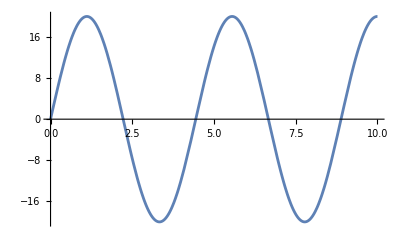

```mathematica
X/.bdy1/.bdy2//FunctionExpand
Plot[%,{t,0,10}]
```